# Laguerre Function. L_n(x)

```mathematica
LaguerreL[0, x]
```

1

```mathematica
LaguerreL[1, x]
```

1-x

```mathematica
LaguerreL[2, x]
```

1/2 (2-4 x+x^2)

```mathematica
LaguerreL[3, x]
```

1/6 (6-18 x+9 x^2-x^3)

```mathematica
FewLaguerres = Table[LaguerreL[n, x], {n, 0, 5}]
```

{1,1-x,1/2 (2-4 x+x^2),1/6 (6-18 x+9 x^2-x^3),1/24 (24-96 x+72 x^2-16 x^3+x^4),1/120 (120-600 x+600 x^2-200 x^3+25 x^4-x^5)}

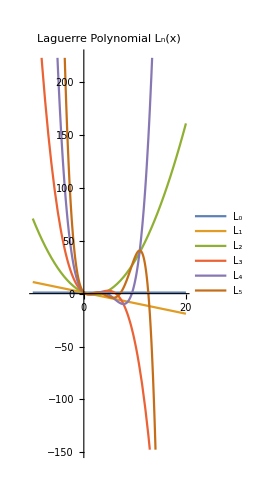

```mathematica
Plot[FewLaguerres, {x, -10, 20}, PlotLabel->"Laguerre Polynomial L_n(x)", PlotLegends->{Table[Subscript[L, n],{n, 0, 5} ]},AspectRatio->Full]
```

```mathematica
"interactive plot"%92DynamicModule[{xc,dx},Manipulate[Plot[FewLaguerres,{x,xc-dx,xc+dx},PlotLabel->"Laguerre Polynomial \!\(\*SubscriptBox[\(L\), \(n\)]\)(x)",PlotLegends->{Table[Subscript[L, n],{n,0,5}]},AspectRatio->Full],{{xc,5,"center"},-85,95},{{dx,15.,"zoom"},90,0.9}],DynamicModuleValues:>{}]
```

Note that the Subscript[L, 1] has its first and only minimum at x -> +∞ . Also, the first minimum of each Laguerre polynomial shift towards the origin with increasing order, while magnitude of its first minimum (its depth below the abscissa) decreases towards zeros with increasing order . Further, L_1  has its first and only maximum at x -> -∞ . Subscript L_0 has no extremum. L_2 has maxima at x -> + ∞ .
From L_3 onwards, Laguerre polynomials have finite first maximum with the feature that the higher the order the later the occurrence of the first maximum and the larger the magnitude of the maximum . 
Simply, from L_3 onwards, a higher Laguerre polynomials attains its first maximum before the Laguerre Polynomial of order lower that its and that too with smaller magnitude of maximum than a polynomial of lower order. For instance, it is evident from the interactive plot that L_3 attains its larger first maximum only after L_3 has attained its smaller first maximum, which occurred only and only after L_5 has attained its much smaller first maximum already, and so forth.